```mathematica
A={{3,-1},{2,3}};
b={1,-1};
```

```mathematica
A//MatrixForm
```

(3 | -1
2 | 3)

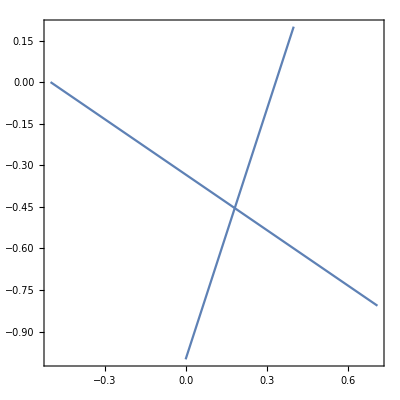

```mathematica
gr=ContourPlot[A.{x,y}==b,{x,-0.5,0.71},{y,-1,0.2},Axes->True]
```

```mathematica
d=IdentityMatrix[2]*A;
```

```mathematica
d//MatrixForm
```

(3 | 0
0 | 3)

```mathematica
c=Inverse[d].(d-A);
```

```mathematica
c//MatrixForm
```

(0 | 1/3
-2/3 | 0)

```mathematica
xt=LinearSolve[A,b]//N;
```

```mathematica
Norm[c,∞]
```

2/3

```mathematica
(*b1=Inverse[d/ω-l].b;*)
```

```mathematica
(*j=1;*)
```

```mathematica
(*xpr={{0,0}};*)
```

```mathematica
(*While[Norm[xpr[[j]]-xt]>0.0001,xpr=Append[xpr,c.xpr[[j]]+b1];j++];*)
```

```mathematica
(*j*)
```

```mathematica
xpr={{0,0}};
```

```mathematica
x1=xpr[[1]][[1]];
x2=xpr[[1]][[2]];
k=0;
```

```mathematica
While[Norm[xpr[[-1]]-xt]>0.0001,t=x1;x1=1/(A[[1]][[1]])(b[[1]]-A[[1]][[2]] x2);xpr=Append[xpr,{x1,x2}];
x2=1/(A[[2]][[2]])(b[[2]]-A[[2]][[1]] t);xpr=Append[xpr,{x1,x2}];k++];
```

```mathematica
k
```

12

```mathematica
ω=1.1;
```

```mathematica
While[Norm[xpr[[-1]]-xt]>0.0001,x1=(1-ω)x1-ω (A[[1]][[2]])/(A[[1]][[1]]) x2+ω b[[1]]/(A[[1]][[1]]);xpr=Append[xpr,{x1,x2}];
x2=(1-ω)x2-ω(A[[2]][[1]])/(A[[2]][[2]])x1+ω b[[2]]/(A[[2]][[2]]);xpr=Append[xpr,{x1,x2}];k++];
```

```mathematica
(*МЕТОД ЯКОБИ*)
```

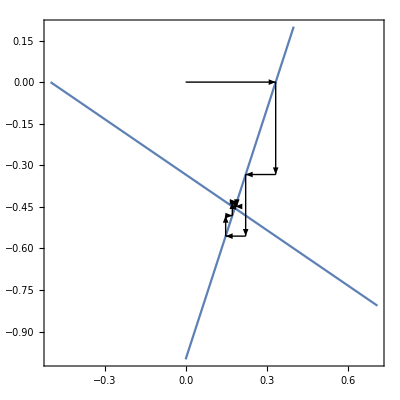

```mathematica
Show[gr,Graphics[{Arrowheads[0.015],Table[Arrow[{xpr[[i]],xpr[[i+1]]}],{i,1,k}]}]]
```

```mathematica
(*МЕТОД ЗЕЙДЕЛЯ*)
```

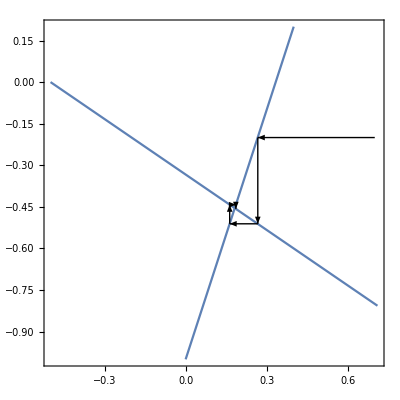

```mathematica
Show[gr,Graphics[{Arrowheads[0.015],Table[Arrow[{xpr[[i]],xpr[[i+1]]}],{i,1,k}]}]]
```

```mathematica
(*МЕТОД РЕЛАКСАЦИИ*)
```

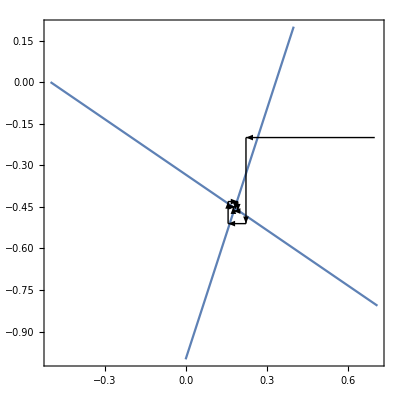

```mathematica
Show[gr,Graphics[{Arrowheads[0.015],Table[Arrow[{xpr[[i]],xpr[[i+1]]}],{i,1,k}]}]]
```